# KASUS TOV SCgrav Ho-Matsuo (juga pakai constant energy density)

## Pers gerak

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify
limitαnol-> Solve[(persν/.{α->0})==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→-(2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α},{ν'[rs]→(2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α}}

limitαnol→{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])/(8 r[rs])}}

```mathematica
rootpertama-> Series[-1/α 2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
rootkedua-> Series[1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
```

rootpertama→-(2 (r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))+(√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2 α)/(4 r[rs]^4 r'[rs]^4)+O[α]^2

rootkedua→(2 (-r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))-((√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2) α)/(4 (r[rs]^4 r'[rs]^4))+O[α]^2

### Jadi pers geraknya yg bisa ditulis eksplisit adalah

```mathematica
pers1:=ν'[rs]-> 1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))
(*Persamaan differensial metrik*)
pers2:=r''[rs]-> 1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ r[rs]^2 ρ0-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])(*Persamaan differensial radius*)
```

```mathematica
pers2/.{pers1,D[pers1,rs]}//Simplify
```

r''[rs]→1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+(8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α+(4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2)/α-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))))

```mathematica
Solve[r''[rs]==1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+(8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α+(4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2)/α-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))),r''[rs]]//Simplify
```

{{r''[rs]→1/(4 (α-r[rs]^2) r'[rs])(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)-2 ⅇ^ν[rs] (2 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))-α ν'[rs])+ⅇ^(ν[rs]/2) κ (-p0+2 ⅇ^(ν[rs]/2) ρ0) r[rs]^2 (2 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))-α ν'[rs]))}}

### Membandingkan dengan persaman TOV GR

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+0α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+0α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 0 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])}}

```mathematica
pers3:=ν'[rs]-> (ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])
(*Persamaan differensial metrik*)
pers4:=r''[rs]->(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])
(*Persamaan differensial radius*)
pers4/.{pers3}//Simplify
```

r''[rs]→((ⅇ^(ν[rs]/2) p0 κ-2 ⅇ^ν[rs] κ ρ0) r[rs]^2+2 (ⅇ^ν[rs]-r'[rs]^2))/(2 r[rs])

### Backward calculation Ho-Matsuo

```mathematica
Clear["Global`*"]
pers1=-ν'[rs]+1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)));
(*Persamaan differensial metrik*)
pers2=-r''[rs]+1/(4 (α-r[rs]^2) r'[rs])(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)-2 ⅇ^ν[rs] (2 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))-α ν'[rs])+ⅇ^(ν[rs]/2) κ (-p0+2 ⅇ^(ν[rs]/2) ρ0) r[rs]^2 (2 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))-α ν'[rs]));(*Persamaan differensial radius*)
```

```mathematica
GS=1.325*10^-12; MSS= 1.1155 * 10^15;
```

```mathematica
Solve[-60.==x+10.Log[x/10.-1.],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→10.0091}}

{{ν→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>],r→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>]}}

-Graphics-

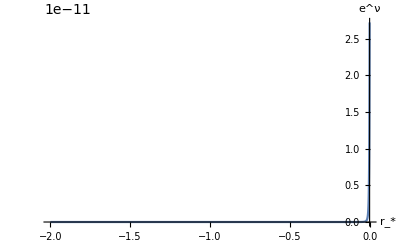

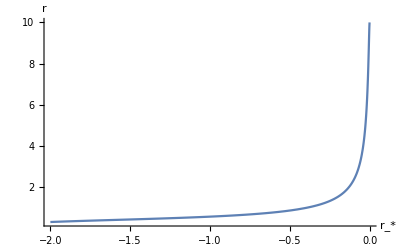

0.316343

2.29323×10^16

```mathematica
α=0.05;
κ =8π GS;
a0:=10.
ρ00:=18.076*10^0 
R:=10./0.9999999999728
rn=-20000000;
rs0=R+a0 Log[R/a0-1];
ν0=Log[1-a0/R];
ρ0=ρ00/κ;
p0=ρ00/κ Exp[ν0/2.];
s=NDSolve[{pers1==0,pers2==0,ν[rs0]==ν0,r[rs0]==R,r'[rs0]==(1-a0/R)},{ν,r},{rs,rs0,rn}]
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
Po[rs_]:=-ρ0 +p0 Exp[-νo[rs]/2]

xx=rn;
Plot[Po[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[Exp[νo[rs]],{rs,xx,rs0},AxesLabel->{"r_*","e^ν"},PlotRange->All]
Plot[ro[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]

ro[rn]
Po[rn]
```

```mathematica
0.31634329999462263/Sqrt[0.05]
```

1.41473

#### Hasil ini sesuai dengan solusi eksterior

```mathematica
R-a0
```

2.71999×10^-10

```mathematica
rs0
```

-233.278

-48.4014

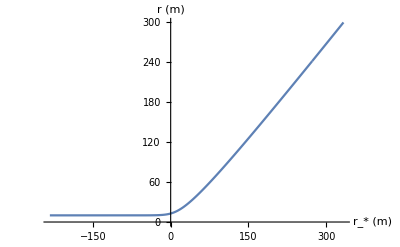

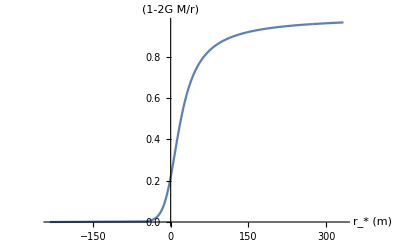

```mathematica
x[i_]:=R+i (300-R)/10000
x[1]+10.Log[x[1]/10.-1]
tabel=Table[{x[i]+10.Log[x[i]/10.-1],x[i]},{i,0,10000}];
ListLinePlot[tabel,PlotRange->All,AxesLabel->{"r_* (m)","r (m)"}]
tabel2=Table[{x[i]+10.Log[x[i]/10.-1],1-10./x[i]},{i,0,10000}];
ListLinePlot[tabel2,PlotRange->All,AxesLabel->{"r_* (m)","(1-2G M/r)"}]
```

```mathematica
tabel[[1]]
tabel2[[1]]
```

{-233.278,10.}

{-233.278,2.72×10^-11}

### Forward

{{ν→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>],r→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>]}}

-Graphics-

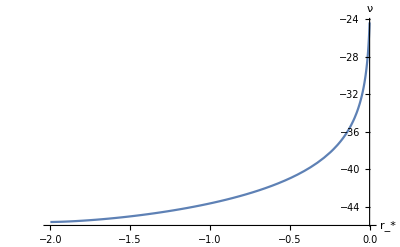

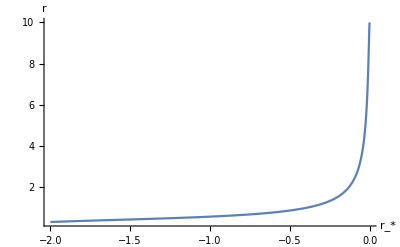

```mathematica
s1=NDSolve[{pers1==0,pers2==0,ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]},{ν,r},{rs,rn,rs0}]
νo1[rs_]=Evaluate[ν[rs]/.s1][[1]];
ro1[rs_]=Evaluate[r[rs]/.s1][[1]];
Po1[rs_]:=-ρ0 +p0 Exp[-νo1[rs]/2]

xx=rn;
Plot[Po1[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νo1[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[ro1[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Perbandingan Backward vs Forward

-Graphics-

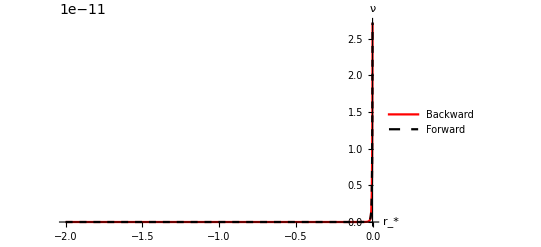

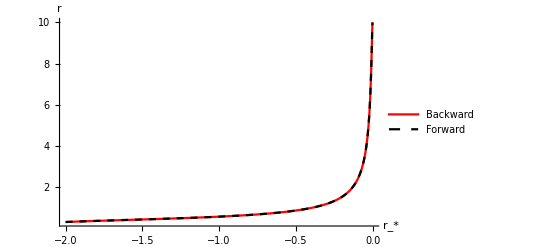

```mathematica
Plot[{ Po1[rs], Po[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","P"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
Plot[{Exp[νo1[rs]],Exp[νo[rs]]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","ν"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
Plot[{ro1[rs],ro[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_*","r"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward","Forward"}]
```

### Perbandingan Backward vs Forward

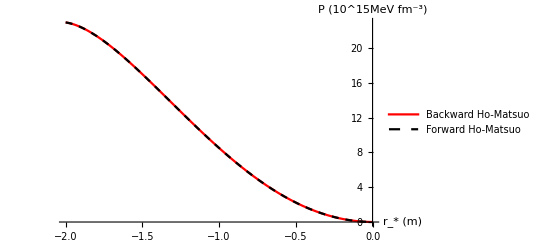

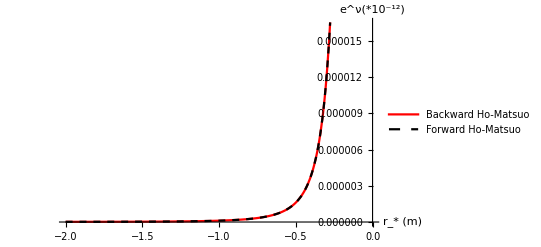

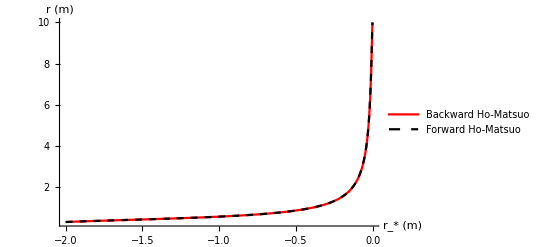

```mathematica
Plot[{Po[rs]*10^-15, Po1[rs]*10^-15},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","P (10^15MeV fm^-3)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
Plot[{Exp[νo[rs]]*10^12,Exp[νo1[rs]]*10^12},{rs,rn,rs0},PlotRange->Automatic,AxesLabel->{"r_* (m)","e^ν(*10^-12)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
Plot[{ro[rs],ro1[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","r (m)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
```

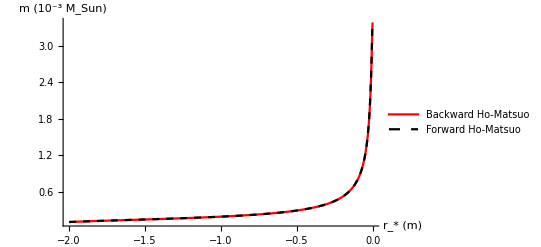

```mathematica
mo[rs_]:=ro[rs]/(2GS MSS)(1-ro'[rs])
mo1[rs_]:=ro1[rs]/(2GS MSS)(1-ro1'[rs])
Plot[{mo[rs]*10^3,mo1[rs]*10^3},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","m (10^-3 M_Sun)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
```

Keluarin datanya

```mathematica
R-a0
```

2.71999×10^-10

```mathematica
ClearAll[x]
x[i_]:=rn+i(rs0-rn)/1000
data:=Table[{x[i]/100000,Po[x[i]]*10^-15, Po1[x[i]]*10^-15,mo[x[i]]*10^3, mo1[x[i]]*10^3,Exp[νo[x[i]]]*10^12,Exp[νo1[x[i]]]*10^12,ro[x[i]], ro1[x[i]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-5.1.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-5.1.dat